## 7/3 Progress

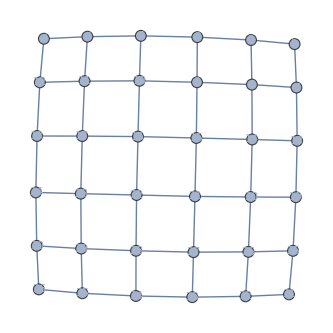

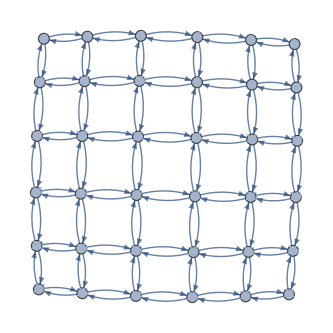

```mathematica
squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[i*n+j<-> i*n+j+1, {j, 1, n-1}], {i, 0, n-1}], Table[Table[i*n+j<-> i*n+j+n, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25, EdgeWeight->{_->1}];

squareDirectedGraph[n_Integer]:=
Graph[Flatten[{Table[Table[{i*n+j-> i*n+j+1, i*n+j+1-> i*n+j}, {j, 1, n-1}], {i, 0, n-1}], Table[Table[{i*n+j-> i*n+j+n, i*n+j+n-> i*n+j}, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25];

myGraph = squareGraph[6]
myDirectedGraph = squareDirectedGraph[6]
```

I made two visualization of a common road structure in cities: a grid like structure of “blocks” of approximately equal length roads. The intersections, which can be marked by traffic lights, are labeled from 1 to 36 and serve as the nodes, while the edges are the roads. The undirected graph above is similar to the directed graph below because splitting a bi-directional road into two equal but opposite directions are essentially equal.

I played with some formatting too, including making sure that the edges are weighted with 1, but not labeled (or else it will look too disgusting). I also aligned the vertex number label to be centered and vertex size to be 1/4 of its intended size. 

The generation involves two nested Table structures, joined by Flatten. The first nest runs through all but the right column of the grid to generate horizontal edges, and ths

```mathematica
findLengthKPath[k_Integer, st_Integer]:=
Module[{rando := RandomSample[Range[36]]},
candidatePaths = Table[FindPath[myGraph, st, rando[[i]], {k}], {i, 1, 36}];
Select[candidatePaths, Length[#]>0&, 1]
]
```

{1,2,3,4,5,6,12,11,17,18,24}

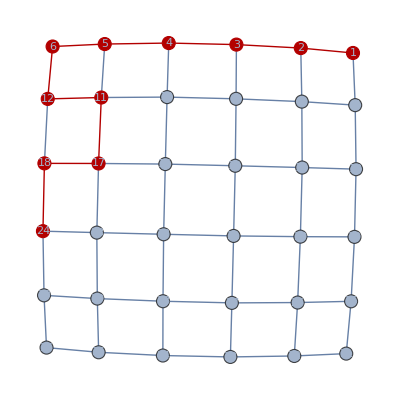

```mathematica
foundPath = Flatten[findLengthKPath[10, 1]]
HighlightGraph[myGraph, PathGraph[foundPath]]
```